```mathematica
If[!NumberQ[makePallette],NotebookEvaluate[NotebookDirectory[]~~"visualVocabDefs.nb"],NotebookEvaluate[NotebookDirectory[]~~"vvClear.nb"]];
```

## Inside Filters

```mathematica
credits
```

This notebook is part of A Visual Vocabulary for Image Processing. All rights are reserved by the authors, W. A. Sethares and C. R. Johnson, Jr. Last revised Jan 2017. All x-ray images are used with permission of the Van Gogh Museum and the Rijksmuseum, Amsterdam, The Netherlands. Please do not violate the trust of the museums that have provided access to their x-ray images by distributing this data in any form.

Underlying the ideas of correlation, filtering, and transforms is the idea of the angle (or inner product) between two signals.

```mathematica
TableForm[{{Hyperlink["HighPassXRay",{"vvInsideFilters.nb","labelHighPassXRay"}],labelHighPassXRay},{Hyperlink["MeanFiltFreqResp",{"vvInsideFilters.nb","labelMeanFiltFreqResp"}],labelMeanFiltFreqResp},{Hyperlink["GaussFreqResp",{"vvInsideFilters.nb","labelGaussFreqResp"}],labelGaussFreqResp}}]
```

| Filtering x-ray tiles with the Sobel highpass filter
 | Frequency response of the mean filter with varying orders
 | Frequency response of a Gaussian filter with varying orders

The discrete delta function δ[k], useful in characterizing the behavior of linear time invariant systems, is the sequence that is 0 for all k except for δ[0]=1. An arbitrary discrete-time signal can be written as a linear combination of such pulses. For instance, if w[k] is the repeating pattern {-1,1,2,1,-1,1,2,1...} it can be written

w[k] = - δ[k] + δ[k-2] + 2 δ[k-2] + δ[k-3] - δ[k-4] + δ[k-5] + 2 δ[k-6] + δ[k-7]...

In general, the discrete-time signal w[k] can be written

w[k]=∑_(j=-∞)^∞ w[j] δ[k-j].

Discrete time systems map input signals into output signals. Such systems are characterized by a kernel (also called an impulse response) that h[k], which is the output when the input happens to be the discrete delta function δ[k]. When an input x[k] is more complicated than a single pulse, the output y[k] can be calculated by summing all the responses to all the individual terms. This process is called the convolution of h[k] and x[k] and is written

y[k]=∑_(j=-∞)^∞ x[j] h[k-j] = x[k]*h[k]

The process of linear filtering is demonstrated graphically in this demo, in which a yellow kernel is passed across a green data sequence to give a blue (filtered) output. There are many ways to implement this linear filtering. Here we compare six different ways to filter data x with a kernel h: convolution, correlation, using the frequency domain method, two direct time domain methods, and using the inner product directly. The only difference (other than numerical factors) is in the way edge conditions are handled with padding.

```mathematica
h = {1, -1,2,-2,3, -3}; 
x = {1,2,3,4,5,6, -5, -4, -3, -2, -1};  
n = Length[x]+Length[h]-1;
xPad = PadRight[x,n];
```

In the convolution method, the kernel h is thought of as the impulse response of a linear time-invariant system and the x is thought of as the input to that system. The convolution yConv is then the output of the system.

```mathematica
yConv = ListConvolve[h,x,{1,1},0]
yConvPad= ListConvolve[h,xPad,{1,1}]
```

{1,1,3,3,6,6,-6,6,-18,6,-30}

{1,1,3,3,6,6,-6,6,-18,6,-30,6,5,5,3,3}

In the correlation method, the kernel h is thought of as a marker or mask and x is thought of as the data that is to be examined. The correlation yCorr is then how much like x the kernel is at each place in the sequence.

```mathematica
yCorr = ListCorrelate[Reverse[h],x,{-1,-1},0]
yCorrPad = ListCorrelate[Reverse[h],xPad,{-1,-1}]
```

{1,1,3,3,6,6,-6,6,-18,6,-30}

{1,1,3,3,6,6,-6,6,-18,6,-30,6,5,5,3,3}

The Fourier method exploits the fact from Fourier Transforms that the product of the transforms is equal to the convolution of the time domain signals. The following calculate the Fourier transform of h (ffth) and the Fourier transform of x (fftx), after padding to the same length. The element-by-element product is then inverse transformed, giving yFourier. which is numerically the same as the above methods.

```mathematica
ffth = Fourier[PadRight[h,n],FourierParameters->{1,-1}];
fftx =  Fourier[PadRight[x,n],FourierParameters->{1,-1}];
yFourier = InverseFourier[ffth fftx,FourierParameters->{1,-1}]
```

{1.+2.22045×10^-16 ⅈ,1.-3.87192×10^-17 ⅈ,3.-4.44089×10^-16 ⅈ,3.-2.22045×10^-16 ⅈ,6.+0. ⅈ,6.+2.05253×10^-16 ⅈ,-6.+0. ⅈ,6.-2.22045×10^-16 ⅈ,-18.-2.22045×10^-16 ⅈ,6.+7.23031×10^-17 ⅈ,-30.+4.44089×10^-16 ⅈ,6.+2.22045×10^-16 ⅈ,5.+0. ⅈ,5.-2.38837×10^-16 ⅈ,3.+0. ⅈ,3.+2.22045×10^-16 ⅈ}

In the time-domain method, the output of the system with impulse response h is calculated once for each time k, as the input takes on all values in x.

```mathematica
z =PadLeft[x,n];
yTim = ConstantArray[0,Length[x]];
Do[
yTim[[k]] = Total[Reverse[h] z[[k;;k+Length[h]-1]]];
,{k,1,Length[x]}];
yTim
```

{1,1,3,3,6,6,-6,6,-18,6,-30}

Here's a time domain version that's like one might program it in Java or C. Normally one would truncate the initial string of zeros.

```mathematica
z = PadLeft[x,n];
yJav = ConstantArray[0,n+1];
Do[ 
Do[
yJav[[k]] = yJav[[k]]+h[[j]] z[[k-j]];
,{j,1,Length[h]}];
,{k,Length[h]+1,Length[x]+Length[h]}];
yJav
```

{0,0,0,0,0,0,1,1,3,3,6,6,-6,6,-18,6,-30}

Using the Inner product

```mathematica
Table[Inner[Times,Reverse[h],z[[i;;i+Length[h]-1]],Plus],{i,1,Length[x]}]
```

{1,1,3,3,6,6,-6,6,-18,6,-30}

Though these methods are more-or-less equivalent, one may be more convenient to use in some applications than in others. In particular, the Fourier method has more far reaching implications than just carrying out the convolution equation.

### Frequency Response: Case Studies

The Sobel filter is used as an example (in the Filters notebook) of how linear filters can have a variety of effects. This section asks what kind of filter the Sobel kernels are. Are they high pass, low pass, band pass, or something else? The answer is that they are a mild kind of high frequency bandpass filter, but the point of the present discussion is to follow a general logical procedure that will allow an answer to this kind of question for any filter. The Sobel kernels can be pictured as

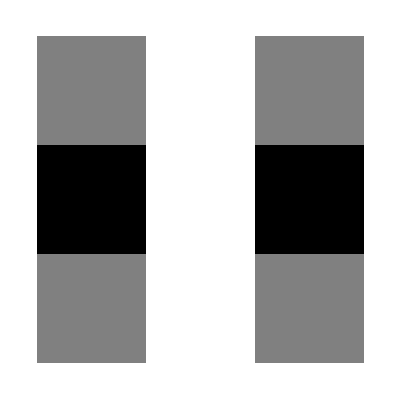
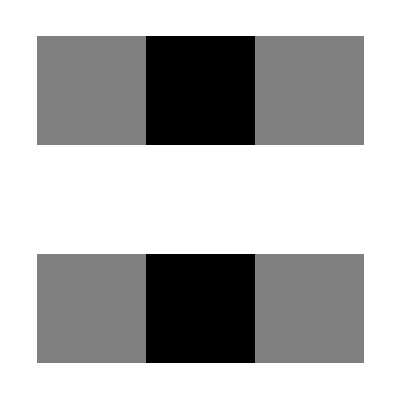
-Graphics--Graphics-Impulse reponse for the Sobel filters in the x and y directions

```mathematica
sobelX={{-1,0,1},{-2,0,2},{-1,0,1}}/4;
sobelY={{1,2,1},{0,0,0},{-1,-2,-1}}/4;
Labeled[Row[{ArrayPlot[sobelX,Frame->False],Spacer[40],ArrayPlot[sobelY,Frame->False]}],"Impulse reponse for the Sobel filters in the x and y directions",LabelStyle->captionStyle]
```

and they can be easily applied to any of the canvas x-rays:

```mathematica
labelHighPassXRay="Filtering x-ray tiles with the Sobel highpass filter";
infoHighPassXRay="Sobel filtering is to a kind of edge detection filter that brings out the most important edges. This occurs because one Sobel filter is a horizontal stripe (emphasizing horizontal features) and the other Sobel filter is a vertical stripe (emphasizing vertical features). The overall method combines these two to locate string horizontal and vertical features.";
Manipulate[img=allImagesXray[[i]];dX=ImageConvolve[img,sobelX];
dY=ImageConvolve[img,sobelY];
ImageAdjust[Image[Sqrt[ImageData[dX]^2+ImageData[dY]^2]]],Row[{Control[{{i,f634Tile,"image"},Thread[Range[numFilesX]->imageNamesX],ControlType->PopupMenu}],Spacer[20],info[infoHighPassXRay]}],FrameLabel->Style[labelHighPassXRay,Medium],TrackedSymbols->{i},SaveDefinitions->saveDef]
```

The frequency response, which shows how the filter reacts to each possible spatial frequency, can be calculated by taking the Fourier transform of the kernel. This is most easily done using the function freqZ2, which takes as arguments the matrix kernel and the two frequency variables.

```mathematica
Labeled[GraphicsRow[{Plot3D[Abs[freqZ2[sobelX,w,v]],{w,-1,1},{v,-1,1},PlotRange->All],Plot3D[Abs[freqZ2[sobelY,w,v]],{w,-1,1},{v,-1,1},PlotRange->All]},ImageSize->Large],"The frequency response of the two Sobel filters",LabelStyle->captionStyle]
```

-Graphics-The frequency response of the two Sobel filters

Both of the Sobel filters have a kind of (nonsymmetrical) band pass character, one operating primarily in the x direction and one in the y direction. It is possible to look at the frequency response of the other linear filters analogously. For instance, the MeanFilter[ ] with a given neighborhood has a frequency response that looks something like a lowpass filter.

```mathematica
labelMeanFiltFreqResp="Frequency response of the mean filter with varying orders";
infoMeanFiltFreqResp="Choose an order and this demonstration plots the frequency response of the mean filter with that order.\n\nFor small orders, the frequency response is very wide, passing most low frequencies without much attenuation and attenuating most higher frequencies.\n\nAs the order increases, the pass band becomes narrower and the range of frequencies attenuate becomes wider.\n\nCan you relate the shapes you see to the Sinc[ ] function?";
Manipulate[meanFilt = ConstantArray[1/meanOrd^2, {meanOrd,meanOrd}]; Plot3D[Abs[freqZ2[meanFilt,w, v]], {w, -1,1}, {v,-1,1}, PlotRange -> All], Row[{Control[{{meanOrd, 3, "order of mean filter"}, 2, 10, 1, Appearance -> "Labeled"}],Spacer[20],info[infoMeanFiltFreqResp]}],
 FrameLabel->Style[labelMeanFiltFreqResp,Medium],TrackedSymbols -> {meanOrd},  SaveDefinitions -> True]
```

which has a low pass character since it passes frequencies near 0 Hz (in both the x and y directions) and attenuates higher frequencies. As the order L of the filter increases, the bandwidth of the filter decreases and the transition regions (from frequencies that are passed to those that are attenuated) becomes narrower. Meanwhile, the frequency response of the GaussianFilter[ ] is similar:

```mathematica
labelGaussFreqResp="Frequency response of a Gaussian filter with varying orders";
infoGaussFreqResp="Choose an order and this demonstration plots the frequency response of a Gaussian filter with that order.\n\nFor small orders, the frequency response is very wide, passing most low frequencies without much attenuation and attenuating most higher frequencies.\n\nAs the order increases, the pass band becomes narrower and the range of frequencies attenuate becomes wider.\n\nThis explains why the blurring with the MeanFilter[] and the blurring with the GaussianFilter[] are so similar in appearance; they are almost the same when viewed as filters in the frequency domain.";
gaussian[n_, m_] := E^(1/12 (-m^2 - n^2))/(12 π);
gaussKernel[eL_] :=  N[Table[gaussian[n, m], {n, -Floor[eL/2], Floor[eL/2]}, {m, -Floor[eL/2],Floor[eL/2]}]];
Manipulate[Plot3D[Abs[freqZ2[gaussKernel[orderG], ω, ν]], {ω,-1, 1}, {ν,-1,1}, PlotRange -> All],Row[{Control[{orderG,3,10,1,Appearance->"Labeled"}],Spacer[20],info[infoGaussFreqResp]}],FrameLabel->Style[labelGaussFreqResp,Medium],TrackedSymbols->{orderG},SaveDefinitions->True]
```

This explains why the blurring with the MeanFilter[ ] and the blurring with the GaussianFilter[ ] are so similar in appearance; they are almost the same when viewed as filters in the frequency domain.